```mathematica
t=Import["~/Desktop/bcs-1.csv"]
bc=Table[{i/4096,Log[t[[i,2]]]},{i,2,Length[t],1}];
```

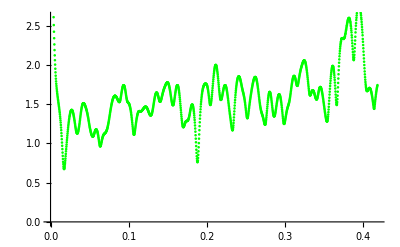

```mathematica
plot1=ListPlot[bc,PlotStyle->Green]
```

```mathematica
t=Import["~/Desktop/bcs-2.csv"]
bc=Table[{i/16384,Log[t[[i,2]]]},{i,2,Length[t],1}];
```

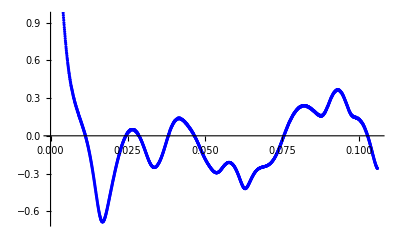

```mathematica
plot2=ListPlot[bc,PlotStyle->Blue]
```

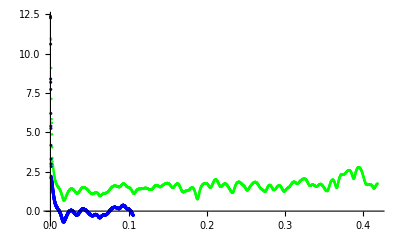

```mathematica
Show[plot1,plot2,PlotRange->Full]
```